```mathematica
Графики начальной функции ее первой и второй производной;
```

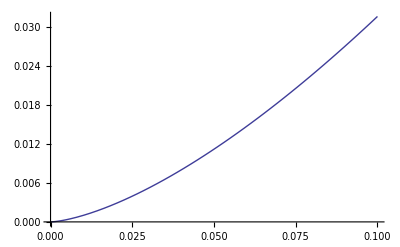

```mathematica
f[x_] := x^(1/2)*Sin[x]
a= 0;
b= 0.1;
Plot[f[x],{x,a,b}]
```

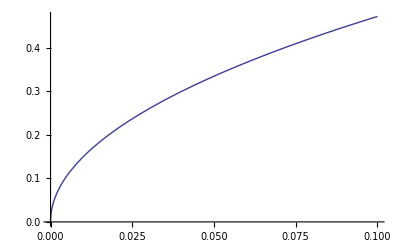

```mathematica
d1=D[f[x],{x,1}];
Plot[d1, {x, a, b}]
```

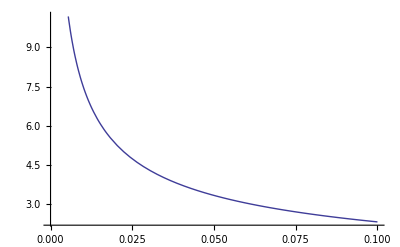

```mathematica
d2=D[f[x],{x,2}];
Plot[d2, {x, a, b}]
```

```mathematica
Ручной рассчет метод симпсона;
```

```mathematica
1 Определяем границы шага интегрирования;
e1 = 0.05;
maxh=e1^0.25
```

0.472871

```mathematica
2 Определяем минимальное необходимое количество шагов;
minn = (b-a)/maxh
```

0.211474

```mathematica
3 Округляем до большего числа кратного 4;
n = 4
```

4

```mathematica
4 Находим шаг интегрирования;
h=(b-a)/n
```

0.025

```mathematica
5 Выполняем рассчет функции на каждом шаге;
x0 = a;
y0 = f[x0];
Print["Шаг 0: x0 = ", x0, ", f[x0] = ", y0]
x1 = x0+h;
y1 = f[x1];
Print["Шаг 1: x1 = ", x1, ", f[x1] = ", y1]
x2 = x1+h;
y2 = f[x2];
Print["Шаг 2: x2 = ", x2, ", f[x2] = ", y2]
x3 = x2+h;
y3 = f[x3];
Print["Шаг 3: x3 = ", x3, ", f[x3] = ", y3]
x4 = x3+h;
y4= f[x4];
Print["Шаг 4: x4 = ", x4, ", f[x4] = ", y4]
```

Шаг 0: x0 = 0, f[x0] = 0

Шаг 1: x1 = 0.025, f[x1] = 0.00395244

Шаг 2: x2 = 0.05, f[x2] = 0.0111757

Шаг 3: x3 = 0.075, f[x3] = 0.0205203

Шаг 4: x4 = 0.1, f[x4] = 0.0315701

```mathematica
6 Выполняем рассчет интеграла c h и 2*h;
resulth = h/3*(y0+4*(y1+y3)+2*y2+y4)
result2h = (2*h)/3*(y0+4*y2+y4)
```

0.0012651

0.00127121

```mathematica
7 Проверка точности по правилу Рунге;
Abs[result2h-resulth]/15
```

4.0726×10^-7

```mathematica
8 Уточнение интеграла при помощи экстрополяции по Ричардсону;

s=1/(2^4-1);
J = result2h+s(result2h-resulth);
result2h - J
```

-4.0726×10^-7

```mathematica
Машинный рассчет методом правых прямоугольников;
```

```mathematica
1 Определение шага интегрирования;
e2 = 0.001;
h2=Sqrt[(24*e2)/((b-a) * 1000)];
n2=Ceiling[(b-a)/h2]
h2=(b-a)/n2
```

7

0.0142857

```mathematica
2 Определение значения интеграла;
result2 = h*Sum[f[a+h*(i)],{i,1,n}]
```

0.00168046

```mathematica
3 Погрешность по правилу Рунге;
result22h = (h/2)*Sum[f[a+(h/2)*(i)],{i,1,n*2}]
runge = result2 - result22h
```

0.00146676

0.000213703

```mathematica
4 Остаточный член;
Plot[f[x],{x,a,b}]
(h(b-a))/2 f[b]
```

-Graphics-

0.0000394626

```mathematica
5 Уточнение интеграла при помощи экстрополяции по Ричардсону;

s=1/(2^4-1);
J = result2+s(result22h-result2)
```

0.00166622

```mathematica
Рассчет интеграла средствами Mathematica;

Jt=N[Integrate[f[x],{x,a,b}]]
```

0.00126374

```mathematica
Машинный рассчет методом Ньютона;
1 Определение шага интегрирования;
a=0.02
h=((80*e2)/((b-a)*9935.96))^(1/4)
n= Ceiling[(b-a)/h]
h=N[(b-a)/n]
n=9(**)
h=(b-a)/(3*n)
```

0.02

0.100161

1

0.08

9

0.00296296

```mathematica
2Рассчет интеграла;
```

```mathematica
result1 = 3*h/8*(f[a]+2*Sum[f[a+(3*i)*h],{i,1,n-1}]+3*Sum[(f[a+(i*3-2)*h]+f[a+(i*3-1)*h]),{i,1,n}]+f[b])
```

0.00124111

```mathematica
3Погрешность по правилу Ругне;
h1 = h/2
n1=(b-a)/(3*h1)
```

0.00148148

18.

```mathematica
result2 = 3*h1/8*(f[a]+2*Sum[f[a+(3*i)*h1],{i,1,n1-1}]+3*Sum[(f[a+(i*3-2)*h1]+f[a+(i*3-1)*h1]),{i,1,n1}]+f[b])
```

0.00124111

```mathematica
result1-result2
```

1.06409×10^-10

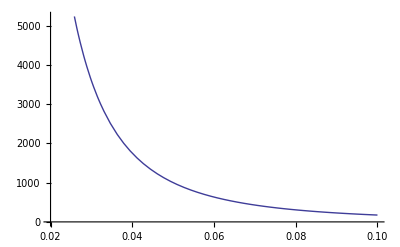

7.65799×10^-10

9935.96

```mathematica
4 Остаточный член;
d4 = D[f[x],{x,4}];
nd4[x_] = d4;
Plot[d4,{x,a,b}]
(h^4(b-a))/80 nd4[a]
nd4[a]
```

```mathematica
5 Уточнение интеграла при помощи экстрополяции по Ричардсону;

s=1/(2^4-1);
J = result1+s(result1-result2)
```

0.00124111

```mathematica
Рекуррентная формула;
M=12;a=0;b=0.1;
T[0]=0.5(b-a)*(f[a]+f[b])
```

0.0015785

```mathematica
Do[h=(b-a)/(2^j);n=2^(j-1);
T[j]=0.5T[j-1]+h*Sum[f[a+(2k-1)*h],{k,n}],{j,1,M}]
Array[T,M,0]
```

{0.0015785,0.00134804,0.00128584,0.00126945,0.0012652,0.00126411,0.00126383,0.00126376,0.00126375,0.00126374,0.00126374,0.00126374}

```mathematica
Do[S[j]=(4T[j]-T[j-1])/3,{j,1,M}]
Array[S,M,1]
```

{0.00127121,0.0012651,0.00126398,0.00126378,0.00126375,0.00126374,0.00126374,0.00126374,0.00126374,0.00126374,0.00126374,0.00126374}

```mathematica
Abs[S[M-1]-Jt]/Jt
```

4.35378×10^-10

```mathematica
k1=(b-a)/4
Do[Tx[i] = a+(i-1)*k1,{i,1,5}];
Array[Tx,5,1]
Do[TA[i,1]=Tx[i];TA[i,2]=f[Tx[i]],{i,1,5}];
Array[TA,{5,2}]
n=5

Do[kr[i,1]=TA[i,2],{i,n}];
Do[Do[kr[i, j + 1] = kr[i+1,j]-kr[i,j],{i,1,n-j}],{j,1,n-1}];
Do[Do[kr[i,j]=0,{j,n-i+2,n}],{i,2,n}]
Array[kr,{n,n}] //MatrixForm

Do[dl2[i]=Abs[kr[i,3]],{i,1,n}];
Do[dl4[i]=Abs[kr[i,5]],{i,1,n}];
Maxdl2=Max[Array[dl2,5,1]]
Maxdl4=Max[Array[dl4,5,1]]
```

0.025

{0.,0.025,0.05,0.075,0.1}

{{0.,0.},{0.025,0.00395244},{0.05,0.0111757},{0.075,0.0205203},{0.1,0.0315701}}

5

(0. | 0.00395244 | 0.00327081 | -0.00114939 | 0.000733067
0.00395244 | 0.00722325 | 0.00212142 | -0.000416327 | 0
0.0111757 | 0.00934466 | 0.00170509 | 0 | 0
0.0205203 | 0.0110498 | 0 | 0 | 0
0.0315701 | 0 | 0 | 0 | 0)

0.00327081

0.000733067